正在构建硬化宇宙 (Steps: 500)...

正在提取物理指标 (脉冲 + 螺旋 + 维度)...

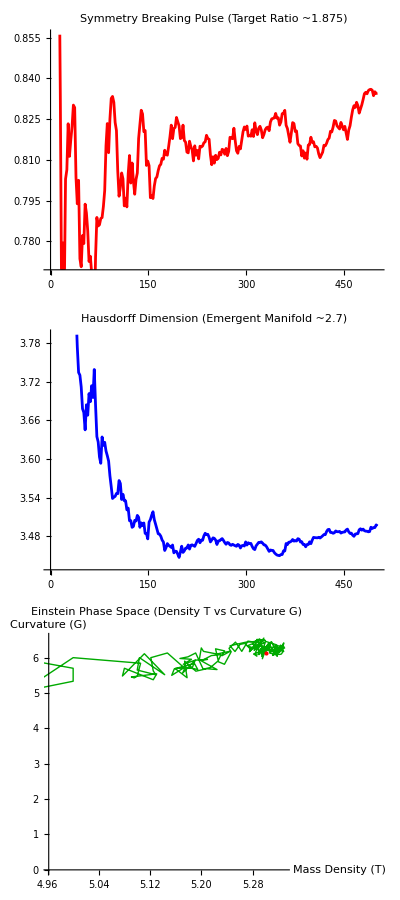
| -Graphics-

-Graphics3D- | -Graphics3D-

```mathematica
(* ==========================================*)(*PART 1:因果硬化规则 (Causal Rigidity)*)(* ==========================================*)(* ==========================================*)(*PART 1:核心规则-因果硬化 (Causal Rigidity)*)(* ==========================================*)(*逻辑：1. 活性边 (无向)="现在"，可以发生反应。2. 惰性边 (有向)="历史"，只负责连接，不再反应。3. 结果：宇宙连接不断，且计算量可控。*)rccRigidStep[g_Graph]:=Module[{allEdges,activeEdges,candidates,selectedPair,e1,e2,x,y,z,w,nextV,newActiveEdges,inertEdges},allEdges=EdgeList[g];
(*关键：只在"无向边"中寻找反应候选者*)activeEdges=Cases[allEdges,_UndirectedEdge];
candidates={};
(*蒙特卡洛采样：防止遍历全图导致卡顿*)Block[{shuffled=RandomSample[activeEdges]},Do[e1=shuffled[[i]];
Do[e2=shuffled[[j]];
If[Length[Intersection[List@@e1,List@@e2]]==1,selectedPair={e1,e2};
Goto["Found"];],{j,i+1,Min[i+20,Length[shuffled]]}],{i,1,Length[shuffled]}]];
Label["Found"];
If[Not[ValueQ[selectedPair]],Return[g]];
{e1,e2}=selectedPair;
y=Intersection[List@@e1,List@@e2][[1]];
x=Complement[List@@e1,{y}][[1]];
z=Complement[List@@e2,{y}][[1]];
nextV=Max[VertexList[g]]+1;
w=nextV;
(*新生成的捷径是"活性"的，代表新的时空泡沫*)newActiveEdges={x<->z,x<->w,w<->z};
(*旧边不删除，而是变为"有向边" (冻结的历史)*)inertEdges={x->y,y->z};
(*构建新图*)Graph[VertexList[g]~Join~{w},Union[Complement[allEdges,{e1,e2}],newActiveEdges,inertEdges]]];

(* ==========================================*)
(*PART 2:演化与数据采集*)
(* ==========================================*)

initG=CycleGraph[4];
steps=500; (*步数*)

Print["正在构建硬化宇宙 (Steps: ",steps,")..."];
results=NestList[rccRigidStep,initG,steps];

Print["正在提取物理指标 (脉冲 + 螺旋 + 维度)..."];

(*物理分析模块*)
analysisData=Table[Module[{gRaw=results[[i]],g,totalM,residM,pulse,dimension,massDensity,ricciK},(*【物理投影】：将混合图视为单纯的几何连接图进行测量*)g=Graph[UndirectedEdge@@@EdgeList[gRaw]];
(*1. 基础度量*)totalM=EdgeCount[g];
(*2. 计算 1.875 脉冲 (对称性破缺指标)*)(*Pulse=TotalEdges/Sum(|Degree-MeanDegree|)*)residM=Total[Abs[VertexDegree[g]-Mean[VertexDegree[g]]]];
pulse=totalM/(residM+1*^-10);
(*3. 豪斯多夫维度 (D)*)dimension=Module[{components=ConnectedGraphComponents[g]},If[Length[components]==0,0,Module[{main=components[[1]]},If[MeanGraphDistance[main]<=1,0,Log[VertexCount[main]]/Log[MeanGraphDistance[main]]]]]];
(*4. 广义相对论参数*)(*T_uv (质量密度)*)massDensity=Mean[VertexDegree[g]];
(*G_uv (拓扑曲率)-使用 TimeConstrained 防止复杂图卡死*)ricciK=TimeConstrained[N[Total[Length/@FindCycle[g,{3},All]]/VertexCount[g]],0.2,0];
{i,pulse,dimension,massDensity,ricciK}],{i,1,Length[results],2}]; (*每2步采样一次*)

(* ==========================================*)
(*PART 3:终极可视化仪表盘*)
(* ==========================================*)

(*图表 1:黄金比率脉冲*)
plotPulse=ListLinePlot[analysisData[[All,{1,2}]],PlotLabel->"Symmetry Breaking Pulse\n(Target Ratio ~1.875)",GridLines->{{},{1.875}},PlotStyle->Red,ImageSize->300];

(*图表 2:豪斯多夫维度*)
plotDim=ListLinePlot[analysisData[[All,{1,3}]],PlotLabel->"Hausdorff Dimension\n(Emergent Manifold ~2.7)",GridLines->{{},{2.7}},PlotStyle->Blue,ImageSize->300];

(*图表 3:爱因斯坦场方程螺旋*)
plotSpiral=ListLinePlot[analysisData[[All,{4,5}]],PlotLabel->"Einstein Phase Space\n(Density T vs Curvature G)",AxesLabel->{"Mass Density (T)","Curvature (G)"},PlotStyle->{Thick,Darker[Green]},Epilog->{PointSize[Large],Red,Point[Last[analysisData[[All,{4,5}]]]]},ImageSize->300];

(*3D 宇宙视图*)
viz3D=Manipulate[Module[{g=results[[step]],currentV},currentV=VertexCount[g];
Graph3D[g,GraphLayout->"SpringElectricalEmbedding",VertexSize->0.2,(*视觉特效：活性层发光，历史层灰暗*)EdgeStyle->{_UndirectedEdge->Directive[Opacity[0.9],White,Thick],(*活性边*)_DirectedEdge->Directive[Opacity[0.15],Gray]           (*惰性边*)},VertexStyle->Function[v,ColorData["Magma"][Rescale[v,{1,currentV}]]],Background->Black,Boxed->False,PlotLabel->Style[Row[{"Gen: ",step," | Nodes: ",currentV,"\nState: ",If[ConnectedGraphQ[Graph[UndirectedEdge@@@EdgeList[g]]],"Connected Manifold","Broken"]}],White,16],ImageSize->400]],{{step,1,"Evolution Time"},1,Length[results],1}];

(*组合输出*)
Grid[{{viz3D,Column[{plotPulse,plotDim,plotSpiral}]}}]
(* ==========================================*)(*终极验证：全息切片分析 (Holographic Slicing)*)(* ==========================================*)(*1. 获取最终状态*)
finalState=results[[-1]]; (*取第 500 步的宇宙*)

(*2. 物理剥离：分离"现在"(Active)与"历史"(Inert)*)
(*Active:正在发生反应的表面 (Boundary)*)
(*Inert:已经固化的历史 (Bulk)*)
activeSlice=Graph[Cases[EdgeList[finalState],_UndirectedEdge]];
historyBulk=Graph[Cases[EdgeList[finalState],_DirectedEdge]];

(*3. 计算切片的维度 (预测：应该比 3.3 低，回到 2.3~2.7)*)
sliceDimension=Module[{components=ConnectedGraphComponents[activeSlice]},If[Length[components]==0,0,Module[{main=components[[1]]},Log[VertexCount[main]]/Log[MeanGraphDistance[main]]]]];

(*4. 视觉对比：左边是切片(Boundary)，右边是整体(Bulk)*)
Grid[{{(*左图：全息边界 (The Holographic Boundary)*)Graph3D[activeSlice,GraphLayout->"SpringElectricalEmbedding",VertexSize->0.2,VertexStyle->Red,EdgeStyle->Directive[Opacity[0.8],Red,Thick],Boxed->False,Background->Black,PlotLabel->Style["The Boundary (Present Slice)\nTarget Dim: ~2.3 - 2.7\nCurrent: "<>ToString[NumberForm[sliceDimension,{3,2}]],White,14],ImageSize->400],(*右图：因果整体 (The Causal Bulk)*)Graph3D[finalState,GraphLayout->"SpringElectricalEmbedding",VertexSize->0.1,VertexStyle->None,EdgeStyle->{_UndirectedEdge->Directive[Opacity[1],Red,Thick],(*表面*)_DirectedEdge->Directive[Opacity[0.05],White]      (*内部支撑*)},Boxed->False,Background->Black,PlotLabel->Style["The Bulk (History + Present)\nStable Dim: ~3.3",White,14],ImageSize->400]}}]
```